```mathematica
sp=(PauliMatrix[1]+PauliMatrix[2]ⅈ)/2;
sm=(PauliMatrix[1]-PauliMatrix[2]ⅈ)/2;
id=IdentityMatrix[2];
kp=KroneckerProduct;
```

```mathematica
Jp=2 dud^2/.dud->d0/(√3);Vdd[θ_,d_]:=(1-3 Cos[θ]^2)/(4π ϵ0 d^3);
Hdd[sep_]=1/2 Vdd[π/2,sep] Jp/2(kp[sp,sm]+kp[sm,sp]);
H4=(Hdd[1.5μm]+ ℏ kp[DiagonalMatrix[{0,2π df}],id])[[{2,3},{2,3}]];
```

```mathematica
Jp=2 dud^2/.dud->d0/(√3);
μm=10^-6;GHz=10^9;μs=10^-6;
d0=QuantityMagnitude[UnitConvert[Quantity[4.75,"Debyes"]]];ϵ0=QuantityMagnitude[UnitConvert[Quantity["Permittivity of free space"]]];
ℏ=QuantityMagnitude[UnitConvert[Quantity["ReducedPlanckConstant"]]//N];
```

```mathematica
pops[replacements_]:=Module[{tSim0,H,ψ,sols,init,p1,p2,p3,p4,c1,c2,c3,c4,SE},
tSim0=tSim//.replacements;
H=Evaluate[H4//.replacements];
ψ[t_]={c1[t],c2[t]};init=ψ[0]=={1,0};SE=ⅈ ψ'[t]==H.ψ[t];
sols=NDSolve[{SE,init},{c1,c2},{t,tSim0},PrecisionGoal->10,MaxSteps->1000000,Method->"StiffnessSwitching"];
{p1,p2}=Abs[#[t μs]/.sols]^2&/@{c1,c2}]
```

```mathematica
rep={tSim->10000μs,df->0};
```

```mathematica
pops[rep]
```

{{Abs[InterpolatingFunction[…][t/1000000]]^2},{Abs[InterpolatingFunction[…][t/1000000]]^2}}

```mathematica
plotStatePop:={popOfTime=pops[rep];ListPlot[ParallelTable[{τ,#[[1]]/.t-> τ}&/@popOfTime,Evaluate[{τ,0,tSim/μs,1/400 tSim/μs}//.rep]]ᵀ,PlotRange->{0,1},PlotLegends->LineLegend[{"p_Feshbach","p_(v = 22)","p_excited","p_ground"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{"Time (μs)","Population"}]}
```

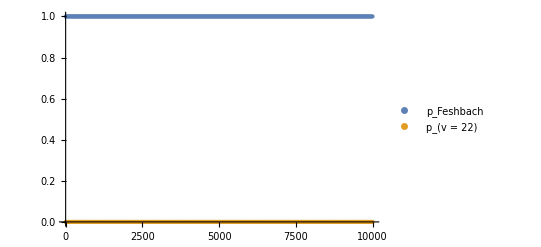

```mathematica
plotStatePop
```

```mathematica
H4
```

{{0.,1.1142×10^-31},{1.1142×10^-31,0.+6.62607×10^-34 df}}